# CKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\alpha goldenratio

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=GoldenRatio;
τ=1;
```

```mathematica
(*randomregion=RandomPoint[Disk[{0,0},1.999],350];*)
(*randomregion=RandomPoint[Disk[{-1.01,0.58},0.01],10];*)
randomregion=Table[{i,0},{i,0,1.999,0.02}];
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=(rot[θ+Pi/4].#&/@randomregion);
randomregion=Join[randomregion,randomregionb];
randomregiondos=Table[{0,i},{i,0,1.999,0.02}];
randomregion=Join[randomregion,randomregiondos];
randomregionc=-randomregion;
randomregion//Length
```

300

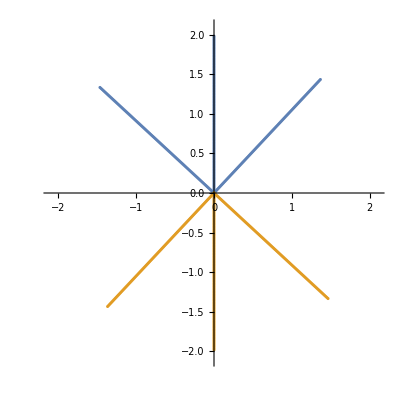

```mathematica
ListPlot[{randomregion,randomregionc},AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1000;
```

```mathematica
α=GoldenRatio;
klist=Table[i,{i,α/20,40α,α/20}];
```

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregionc}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregionc]*(kicks+1),2}];
poincareb=Graphics[{PointSize[0.0010],Red,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

Export["poincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[klist[[j]]]]<>"_kicks_"<>ToString[kicks]<>"_frame"<>ToString[j]<>".png",Show[{poincarea,poincareb}]];
,{j,Length[klist]}]
```

$Aborted

```mathematica
filteredinitial//Length
```

103

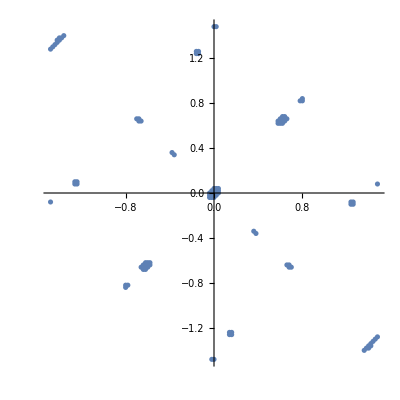

```mathematica
ListPlot[filteredinitial,AspectRatio->1]
```

```mathematica
α=GoldenRatio;
k=20.;
kicks=2000;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,filteredinitial}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[20.],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_filtered_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[20.]]<>"_kicks_"<>ToString[kicks]<>"_frameb"<>ToString[248]<>".png",poincarea];
```

## Powers of Poincaré

```mathematica
Clear[Fun];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];*)
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a},
a=F[α,k,point];
MatrixPower[a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b},
a=F[α,k,point];
b=F[α,k,a.point];
MatrixPower[b.a.mat,p].s
];*)

Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b,c},
a=F[α,k,point];
b=F[α,k,a.point];
c=F[α,k,b.(a.point)];
MatrixPower[c.b.a.mat,p].s
];

Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=GoldenRatio;
τ=1;
```

```mathematica
radius=1.99999;
delta=0.02;
xCoords=Range[0,radius,delta];
yCoords=Range[0,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];*)
circlePoints=Select[gridPoints,Norm[#]<radius&];
(*randomregion=Join[boundaryPoints,circlePoints];
randomregionb=-randomregion;*)
randomregion=circlePoints;
randomregion//Length
```

7949

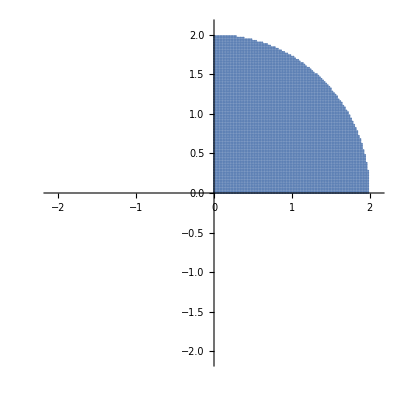

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=800;
k=20.;
p=400;
```

```mathematica
puntosa=ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];poincarec=Graphics[{PointSize[0.001],Blue,Opacity[0.01],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black],Style[", n = ",45,Black],Style[kicks,50,Black],Style[", p = ",45,Black],Style[p,50,Black]}],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_period_4_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>"_p_"<>ToString[p]<>"c.png",poincarec];
```

## Long time series

```mathematica
{q0,p0}={Rationalize[-0.1],Rationalize[1.25]};
```

```mathematica
region=RandomPoint[Disk[{q0,p0},0.01],20];
ListPlot[region,AspectRatio->1]
```

```mathematica
α=GoldenRatio;
k=20.;
kicks=1000000;
puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,k,kicks]],{i,region}];
newpoincarea=ArrayReshape[puntosa,{Length[region]*(kicks+1),2}];
```

```mathematica
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[0.001],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
```

```mathematica
Export["poincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_kicks_"<>ToString[kicks]<>"_frame"<>ToString[1]<>".png",poincarea]
```

# QKT Quantum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\alpha 0.84 and k 20

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
QQ[J_]:=Qp[J]+Transpose[Qp[J]];
PP[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
LaunchKernels[8]
```

{Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8)}

## Method

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(1.99)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

20272

```mathematica
ListPlot[region,AspectRatio->1,ImageSize->350]
```

```mathematica
(*n=20000;
rMax=1.9999;
points=Table[r=Sqrt[i/n]*rMax;
θ=GoldenAngle*i;
{r Cos[θ],r Sin[θ]},{i,n}];
ListPlot[points,AspectRatio->1,Frame->True,PlotStyle->PointSize[0.01]];
region=points;
ListPlot[region];*)
```

```mathematica
n=10000;
rMax=2;
spacing=rMax/Ceiling[Sqrt[n/Pi]];
gridPoints=Flatten[Table[{Rationalize[x],Rationalize[y]},{x,-rMax+spacing,rMax-spacing,spacing},{y,-rMax+spacing,rMax-spacing,spacing}],1];
(*Select points inside the disk and adjust the outermost ones slightly inward*)
points=Select[gridPoints,Norm[#]<rMax&];
points=points/. p_/;Abs[Norm[p]-rMax]<spacing->p*(rMax-spacing)/Norm[p];
region=points;
ListPlot[points,AspectRatio->1,Frame->True,PlotStyle->PointSize[0.005]];
region=points;
```

## Phase space

```mathematica
Clear[J];
J=200;
α=GoldenRatio;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2-Pi])Sz[J]];
```

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],18]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],18]]
];
```

```mathematica
Clear[cohesM];
cohesM=ParallelTable[Quiet[a2iM[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
cohesm=ParallelTable[Quiet[a2im[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimiM,husimim];
husimiM[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesM[[i]]].ψ]^2},{i,Length[region]}];
husimim[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesm[[i]]].ψ]^2},{i,Length[region]}];
```

```mathematica
k=3Pi-Pi/10.;
α=Pi/2;
(*North pole*)
(*mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;*)
mat=Floq[J,α,k,τ];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
q=20;
```

```mathematica
d2M=ParallelTable[Total[Abs[Conjugate[eigenvecM].i]^(2q)],{i,cohesM}];
```

```mathematica
d2m=ParallelTable[Total[Abs[Conjugate[eigenvecm].i]^4],{i,cohesm}];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[J+1]}];
```

```mathematica
newd2m=Transpose[{region[[All,1]],region[[All,2]],-Log[d2m]/Log[J]}];
pr=ParallelTable[1/Total[Abs[Conjugate[eigenvecM].i]^(4)],{i,cohesM}];
newpr=Transpose[{region[[All,1]],region[[All,2]],pr}];
```

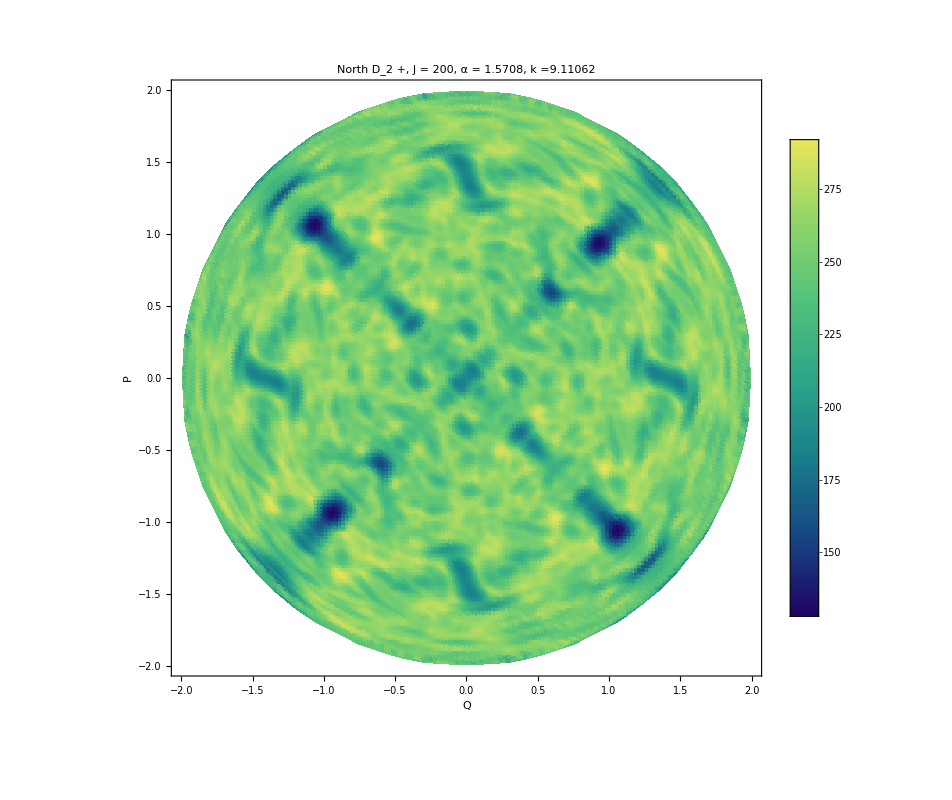

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

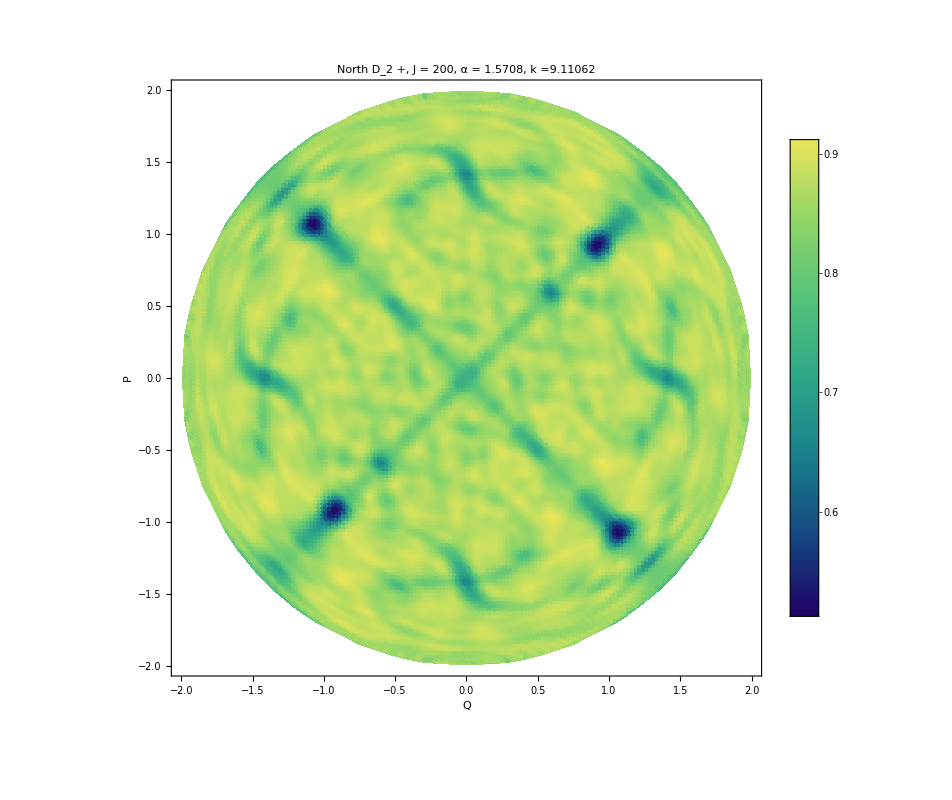

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

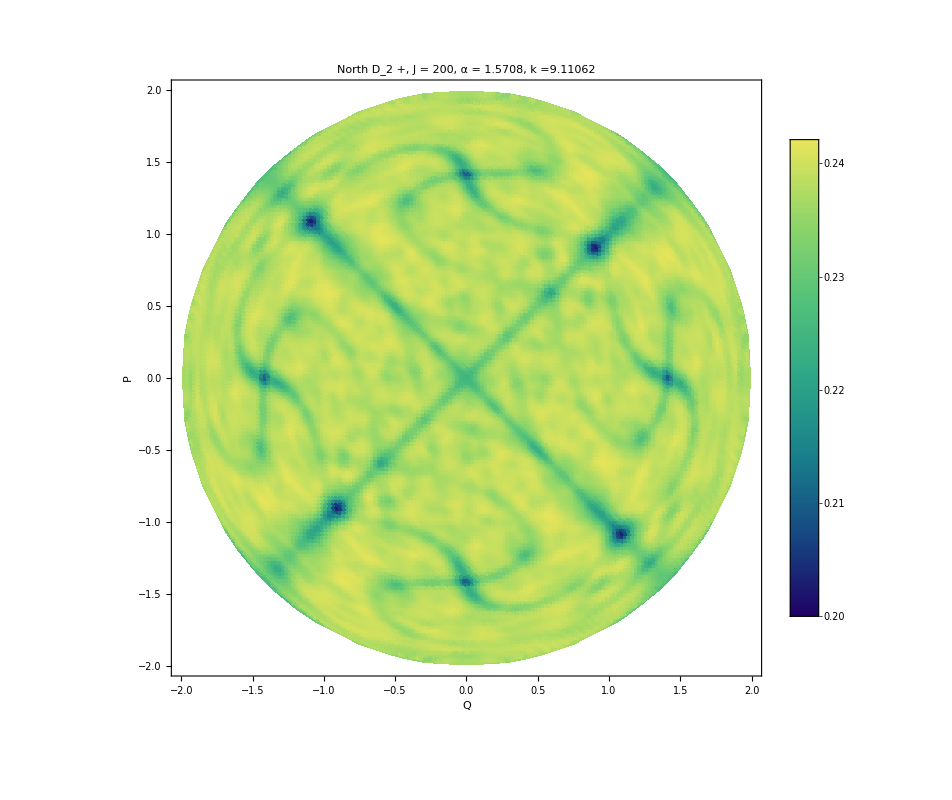

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

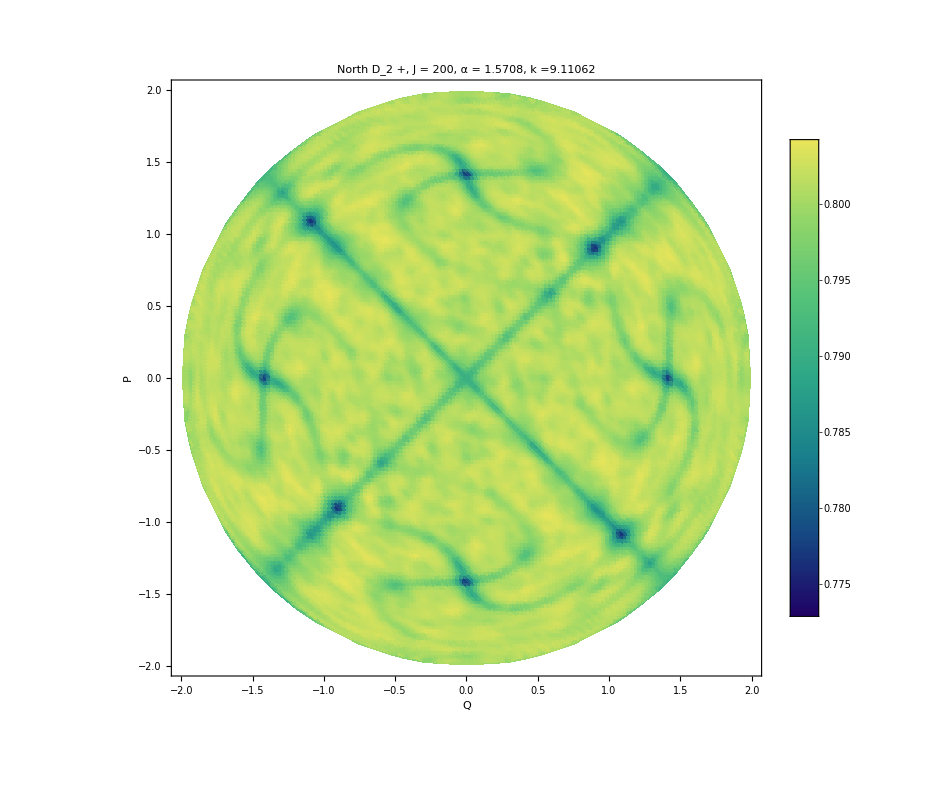

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

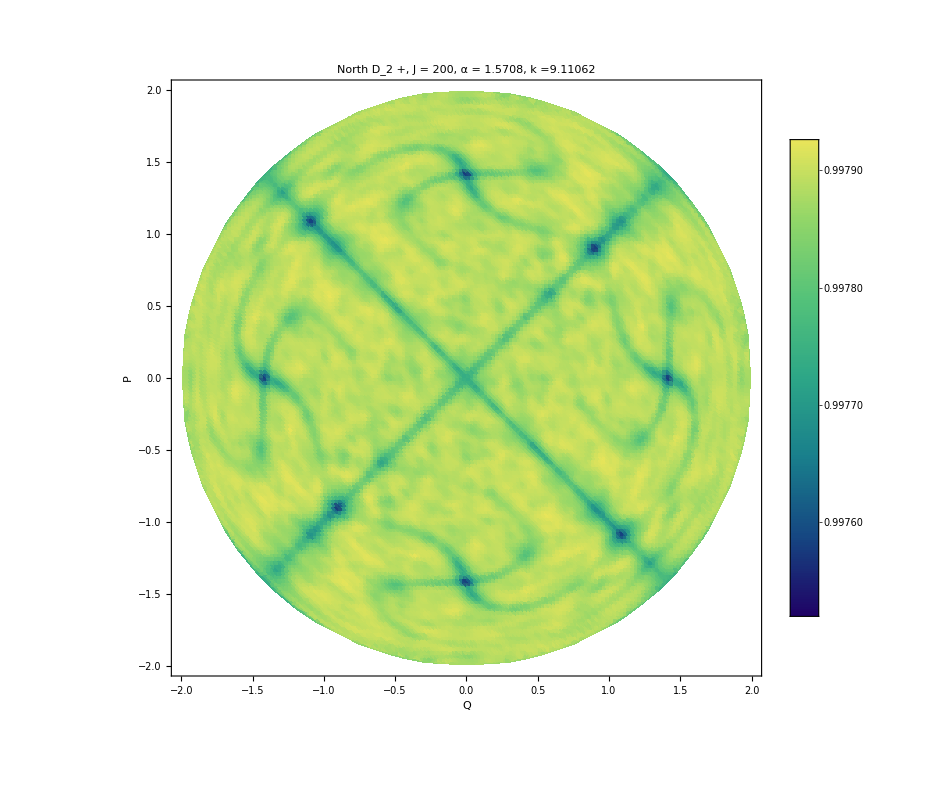

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

```mathematica
d2plotm=ListDensityPlot[newd2m,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2 -, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
```

```mathematica
Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>"_q_"<>ToString[q]<>".png",ListDensityPlot[newd2M,PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North D2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ColorFunction->"BlueGreenYellow",ImageSize->1000]]
Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".m",newd2M]
```

d2plus_zoom_J_509_alpha_1.61803_k_20._dq_delta_q_2.png

d2plus_zoom_J_509_alpha_1.61803_k_20._dq_delta.m

```mathematica
Export["d2minus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[newd2m,PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North D2 -, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]
```

```mathematica
Export["d2minus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".m",newd2m]
```

```mathematica
α=Pi/2;
q=1/10;
k=3Pi-Pi/10.;
```

```mathematica
jlist=Range[300,310];
```

```mathematica
Do[

Clear[cohesM];
cohesM=ParallelTable[Quiet[a2iM[J,i[[1]],i[[2]]]],{i,region}];
cohesm=ParallelTable[Quiet[a2im[J,i[[1]],i[[2]]]],{i,region}];
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
d2M=ParallelTable[Total[Abs[Conjugate[eigenvecM].i]^(2q)],{i,cohesM}];
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[J+1]}];
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[N[k]]<>", q = "<>ToString[N[q]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_dq_"<>ToString[0.035]<>"_q_"<>ToString[N[q]]<>".png",d2plotM];

d2m=ParallelTable[Total[Abs[Conjugate[eigenvecm].i]^(2q)],{i,cohesm}];
newd2m=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2m]/Log[J]}];
d2plotm=ListDensityPlot[newd2m,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D_2 -, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[N[k]]<>", q = "<>ToString[N[q]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
Export["d2minus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_dq_"<>ToString[0.035]<>"_q_"<>ToString[N[q]]<>".png",d2plotm];

,{J,jlist}]
```

$Aborted

## Scaling

```mathematica
iniM=Quiet[a2iM[J,Rationalize[-0.1],Rationalize[1.25]]];
```

```mathematica
upofloqM=Conjugate[eigenvecM].iniM;
```

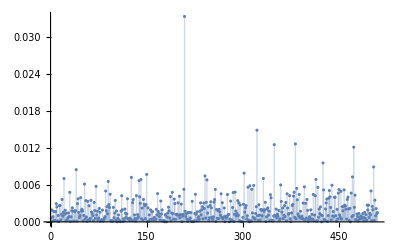

```mathematica
ListPlot[Abs[upofloqM]^2,PlotRange->All,Filling->Axis]
```

```mathematica
jlist=Range[300,700,1];
```

```mathematica
data={};
Do[

upoM=Quiet[a2iM[J,Rationalize[-0.1],Rationalize[1.25]]];mat=Floq[J,α,k,τ];matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
upofloqM=Conjugate[eigenvecM].upoM;
AppendTo[data,{J+1,upofloqM,eigenvalM}];
,{J,jlist}];

Export["ipr_upo_alpha_goldenratio_k_20_j_300_700.m",data]
```

ipr_upo_alpha_goldenratio_k_20_j_300_700.m

```mathematica
ipr=Table[{data[[i,1]],Total[Abs[data[[i,2]]]^4]},{i,Length[data]}];
```

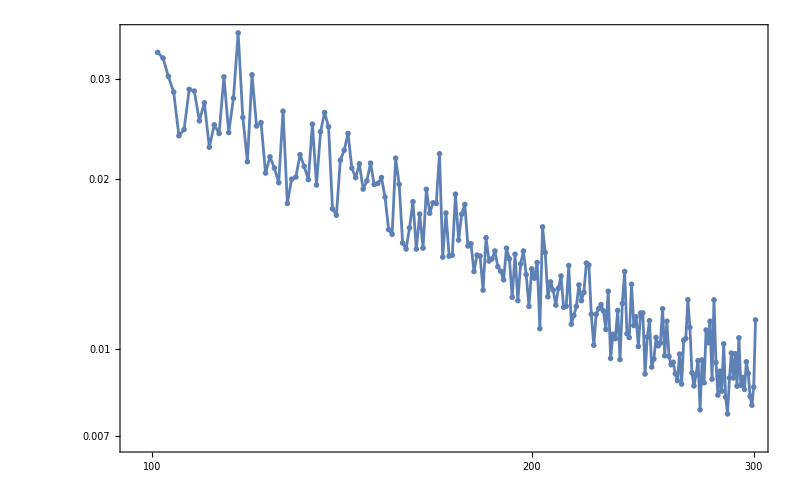

```mathematica
ListLogLogPlot[ipr[[100;;300]],PlotTheme->"Detailed",PlotRange->All,ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers"]
```

```mathematica
wavefunctions=Table[ListPlot[Transpose[{Arg[data[[i,3]]],Abs[data[[i,2]]]^2}],PlotRange->{{-Pi,Pi},{0,0.125}},Filling->Bottom,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["J = "<>ToString[i],25,Black]],{i,50,300}];
```

```mathematica
ListAnimate[wavefunctions,AnimationRunning->False]
```

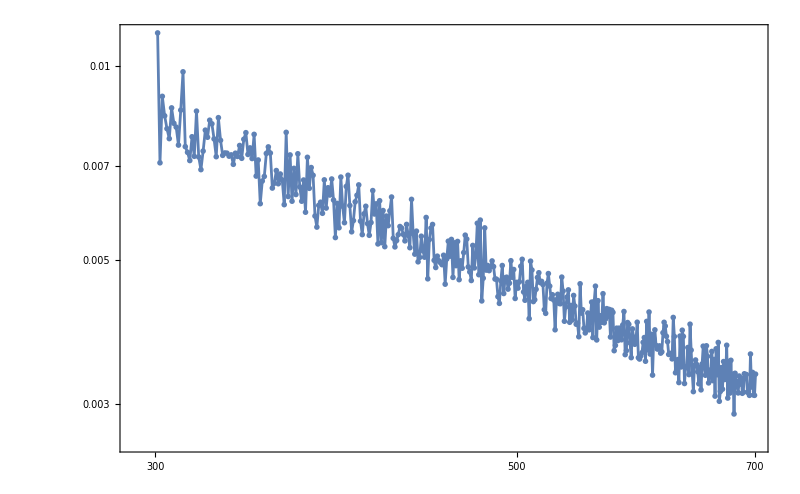

```mathematica
ListLogLogPlot[ipr[[1;;-1]],PlotTheme->"Detailed",PlotRange->All,ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers"]
```

```mathematica
wavefunctions=Table[ListPlot[Transpose[{Arg[data[[i,3]]],Abs[data[[i,2]]]^2}],PlotRange->{{-Pi,Pi},{0,0.035}},Filling->Bottom,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["J = "<>ToString[i],25,Black]],{i,100,200}];
```

```mathematica
ListAnimate[wavefunctions,AnimationRunning->False]
```

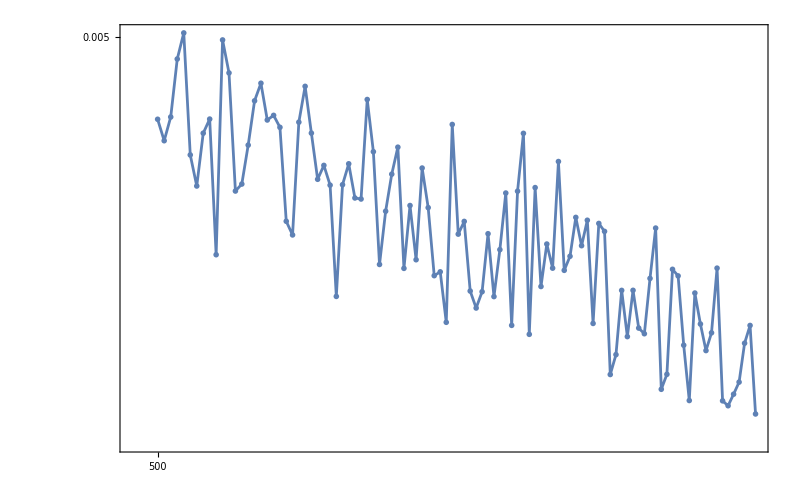

```mathematica
ListLogLogPlot[ipr[[200;;300]],PlotTheme->"Detailed",PlotRange->All,ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers"]
```

```mathematica
wavefunctions=Table[ListPlot[Transpose[{Arg[data[[i,3]]],Abs[data[[i,2]]]^2}],PlotRange->{{-Pi,Pi},{0,0.035}},Filling->Bottom,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["J = "<>ToString[i+300],25,Black]],{i,200,300}];
```

```mathematica
ListAnimate[wavefunctions,AnimationRunning->False]
```

## Husimis

```mathematica
α=GoldenRatio;
τ=1;
k=20.;
J=509;
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
```

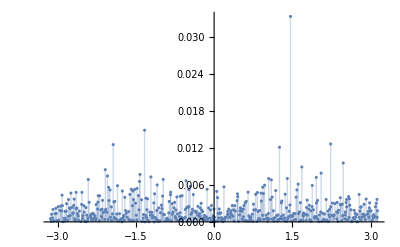

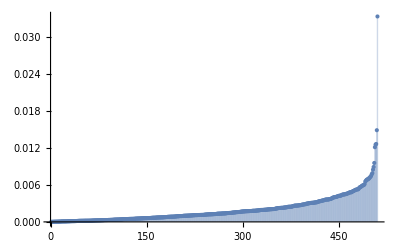

```mathematica
iniM=Quiet[a2iM[J,Rationalize[-0.1],Rationalize[1.25]]];
upofloqM=Conjugate[eigenvecM].iniM;
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloqM]^2}],PlotRange->All,Filling->Axis]
ListPlot[Sort[Abs[upofloqM]^2],PlotRange->All,Filling->Axis]
```

```mathematica
list=Abs[upofloqM]^2;
sorted=Sort[list];
index=Table[Flatten[Position[list,sorted[[i]]]],{i,J+1}];
sortedeigenvecM=Table[eigenvecM[[i[[1]]]],{i,index}];
sortedeigenvalM=Table[eigenvalM[[i[[1]]]],{i,index}];
```

```mathematica
Do[

Export["northeigenvecMas_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[husimiM[sortedeigenvecM[[i]]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec +"<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,-10,-1,1}]
```

## D2 Statistics

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[J+1]}];
```

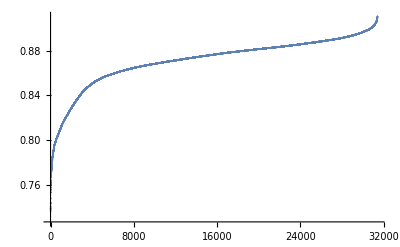

```mathematica
ListPlot[Sort[newd2M[[All,3]]],PlotRange->All]
```

```mathematica
Min[Sort[newd2M[[All,3]]]]
Max[Sort[newd2M[[All,3]]]]
```

0.736541

0.910626

```mathematica
bins=Range[0.72,0.95,0.02]
```

{0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94}

```mathematica
(*Classify data into bins*)
classifiedData=Table[Select[newd2M,bins[[i]]<=#[[3]]<bins[[i+1]]&],{i,Length[bins]-1}];
```

```mathematica
colors=ColorData["Rainbow"]/@Rescale[Most[bins]]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2748607999999999, 0.1822636000000002, 0.7272788000000001],RGBColor[0.24848840000000008, 0.38632640000000046, 0.813373],RGBColor[0.2979596000000002, 0.5657928000000004, 0.7522385999999998],RGBColor[0.3882247999999999, 0.6741949999999999, 0.6035436000000002],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832000000002, 0.7430418, 0.32293539999999993],RGBColor[0.8083416000000001, 0.7110805999999998, 0.2559759999999999],RGBColor[0.8935136000000002, 0.6004149999999995, 0.2205463999999999],RGBColor[0.8929546, 0.3896616000000002, 0.17940080000000005],RGBColor[0.857359, 0.131106, 0.132128]}

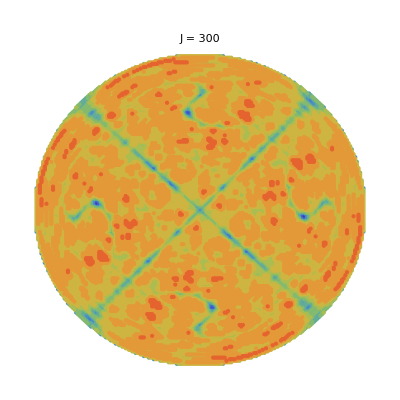

```mathematica
(*Create a density plot for each category*)
Graphics[{Table[{colors[[i]],Point[classifiedData[[i,All,1;;2]]]},(*x,y coordinates*){i,Length[classifiedData]}]},PlotRange->All,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

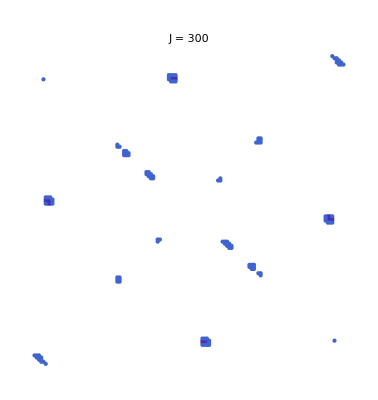

```mathematica
Graphics[{Table[{colors[[i]],Point[classifiedData[[i,All,1;;2]]]},(*x,y coordinates*){i,3}]},PlotRange->All,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

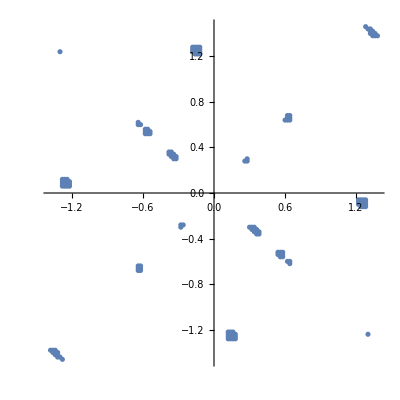

```mathematica
filteredinitial=Transpose[{Flatten[classifiedData[[1;;3]],1][[All,1]],Flatten[classifiedData[[1;;3]],1][[All,2]]}];
ListPlot[filteredinitial,AspectRatio->1]
```

## Dq

```mathematica
qlist={0.05,0.01,6,8};
```

```mathematica
dqdata={};
Do[
dqM=ParallelTable[Total[Abs[Conjugate[eigenvecM].i]^(2q)],{i,cohesM}];
AppendTo[dqdata,dqM];
,{q,qlist}];
```

```mathematica
newdqM=Table[Transpose[{region[[All,1]],region[[All,2]],(1-qlist[[q]])Log[dqdata[[q]]]/Log[J+1]}],{q,Length[dqdata]}];
```

```mathematica
Do[

d2plotM=ListDensityPlot[newdqM[[i]],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3,PerformanceGoal->"Quality",PlotLabel->Style["North D_q +, q = "<>ToString[qlist[[i]]]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True];
Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>"_q_"<>ToString[qlist[[i]]]<>".png",d2plotM];

,{i,Length[newdqM]}]
```

## Differents qkts

```mathematica
Clear[J];
J=300;
α=GoldenRatio;
k=20.;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
(*Clear[floquet];
floquet[J_,α_,k_]:=N[MatrixExp[(-I*k*RandomReal[]/(2J))(Sx[J].Sx[J])+(-I*RandomReal[]*α)(Sx[J])].MatrixExp[(-I*k*RandomReal[]/(2J))(Sy[J].Sy[J])+(-I*RandomReal[]*α)(Sy[J])].MatrixExp[(-I*k*RandomReal[]/(2J))(Sz[J].Sz[J])+(-I*RandomReal[]*α)(Sz[J])]];*)
(*Clear[floquet];
floquet[J_,α_,k_]:=N[MatrixExp[(-I*k*RandomReal[]/(2J))(Sx[J].Sx[J])+(-I*RandomReal[]*α)(Sx[J])].MatrixExp[(-I*k*RandomReal[]/(2J))(Sy[J].Sy[J])+(-I*RandomReal[]*α)(Sy[J])]];*)
Clear[floquet];
floquet[J_,α_,k_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J]+0.5Sy[J].Sy[J])].MatrixExp[(-I*α)(Sz[J])]];
```

```mathematica
k=20.;
mat=floquet[J,α,k];
{eigenvalM,eigenvecM}=Eigensystem[mat];
```

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvecM].i]^(2q)],{i,cohes}];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3,PerformanceGoal->"Quality",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
```

```mathematica
Export["d2_randomtestn_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>"_q_"<>ToString[q]<>".png",d2plotM]
```

d2_randomtestn_J_300_alpha_1.61803_k_20._dq_0.03_q_2.png

```mathematica
ini=a2[J,Rationalize[-1.5],Rationalize[-0.2]];
```

```mathematica
inifloq=Conjugate[eigenvecM].ini;
```

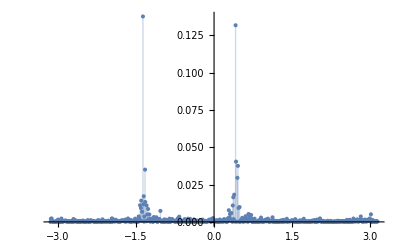

```mathematica
ListPlot[Transpose[{Arg[eigenvalM],Abs[inifloq]^2}],PlotRange->All,Filling->Axis]
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}];
```

```mathematica
list=Abs[inifloq]^2;
sorted=Sort[list];
index=Table[Flatten[Position[list,sorted[[i]]]],{i,2J+1}];
sortedeigenvecM=Table[eigenvecM[[i[[1]]]],{i,index}];
sortedeigenvalM=Table[eigenvalM[[i[[1]]]],{i,index}];
```

```mathematica
Do[

Export["northeigenvecMas_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[husimi[sortedeigenvecM[[i]]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["Random test Eigenvec "<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,-5,-1,1}]
```

## H0

```mathematica
Clear[J];
J=509;
α=GoldenRatio;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2-Pi])Sz[J]];
```

```mathematica
k=20.;
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];
```

```mathematica
ope=Sz[J];
ope1=Table[ope[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
```

```mathematica
h0=ParallelTable[Chop[Conjugate[i].ope1.i],{i,eigenvecM}];
```

```mathematica
list=h0;
sorted=Sort[list];
index=Table[Flatten[Position[list,sorted[[i]]]],{i,J+1}];
sortedeigenvecM=Table[eigenvecM[[i[[1]]]],{i,index}];
sortedeigenvalM=Table[eigenvalM[[i[[1]]]],{i,index}];
```

```mathematica
iniM=Quiet[a2iM[J,Rationalize[-0.1],Rationalize[1.25]]];
upofloqM=Conjugate[eigenvecM].iniM;
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloqM]^2}],PlotRange->All,Filling->Axis]
```

-Graphics-

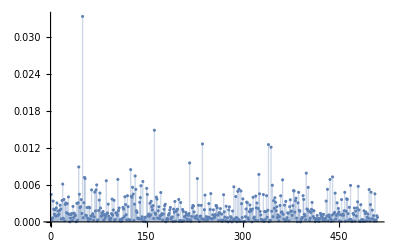

```mathematica
iniM=Quiet[a2iM[J,Rationalize[-0.1],Rationalize[1.25]]];
upofloqM=Conjugate[sortedeigenvecM].iniM;
ListPlot[Abs[upofloqM]^2,PlotRange->All,Filling->Axis]
```

## Survival

```mathematica
Clear[sur];
sur[ini_,n_]:=Module[{a},
Abs[(eigenvalM^n).Abs[ini]^2]^2
];
```

```mathematica
α=GoldenRatio;
τ=1;
k=20.;
J=509;
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
```

```mathematica
iniM=Quiet[a2iM[J,Rationalize[-0.1],Rationalize[1.25]]];
upofloqM=Conjugate[eigenvecM].iniM;
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloqM]^2}],PlotRange->All,Filling->Axis]
ListPlot[Sort[Abs[upofloqM]^2],PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
list=Table[i,{i,0,100,1}];
```

```mathematica
ipr=Total[Abs[upofloqM]^4]
```

0.00498808

```mathematica
Clear[data,data2];
data=ParallelTable[sur[upofloqM,i],{i,list}];
```

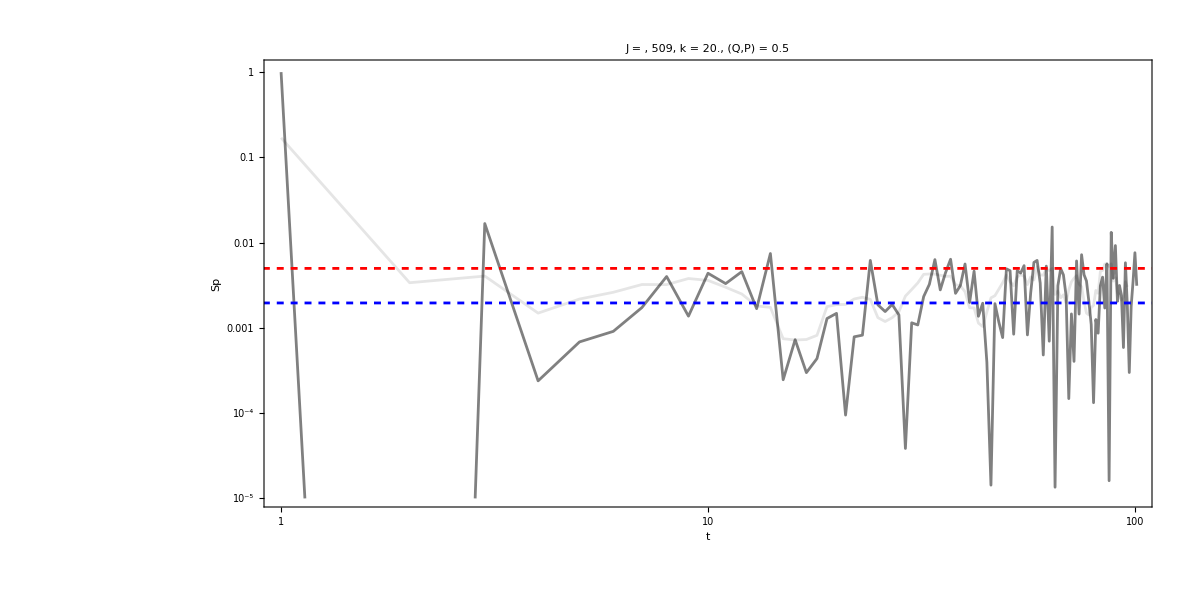

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+5]]],{i,1,Length[data]-5,1}];
plot2=LogLogPlot[{ipr,1/(J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",Joined->True,PlotStyle->{Directive[Gray,Opacity[1]],Directive[Black,Opacity[0.1]]},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[0.5]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

```mathematica
Clear[sur];
sur[ini_,n_]:=Module[{a},
Abs[(eigenvalM^n).Abs[ini]^2]^2
];
J=510;
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
```

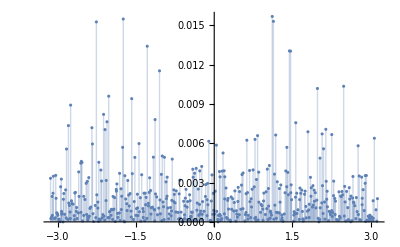

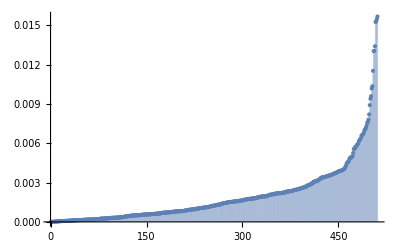

```mathematica
iniM=Quiet[a2iM[J,Rationalize[-0.1],Rationalize[1.25]]];
upofloqM=Conjugate[eigenvecM].iniM;
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloqM]^2}],PlotRange->All,Filling->Axis]
ListPlot[Sort[Abs[upofloqM]^2],PlotRange->All,Filling->Axis]
```

```mathematica
ipr=Total[Abs[upofloqM]^4]
```

0.00483378

```mathematica
Clear[data,data2];
data=ParallelTable[sur[upofloqM,i],{i,list}];
```

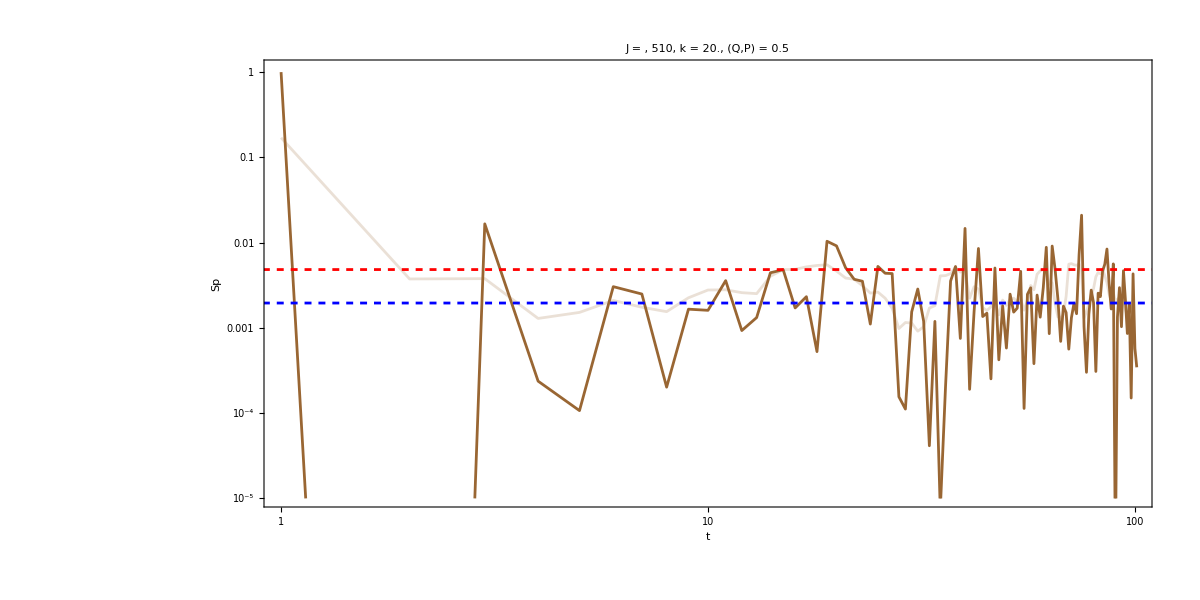

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+5]]],{i,1,Length[data]-5,1}];
plot2=LogLogPlot[{ipr,1/(J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",Joined->True,PlotStyle->{Directive[Brown,Opacity[1]],Directive[Brown,Opacity[0.2]]},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[0.5]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival2=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

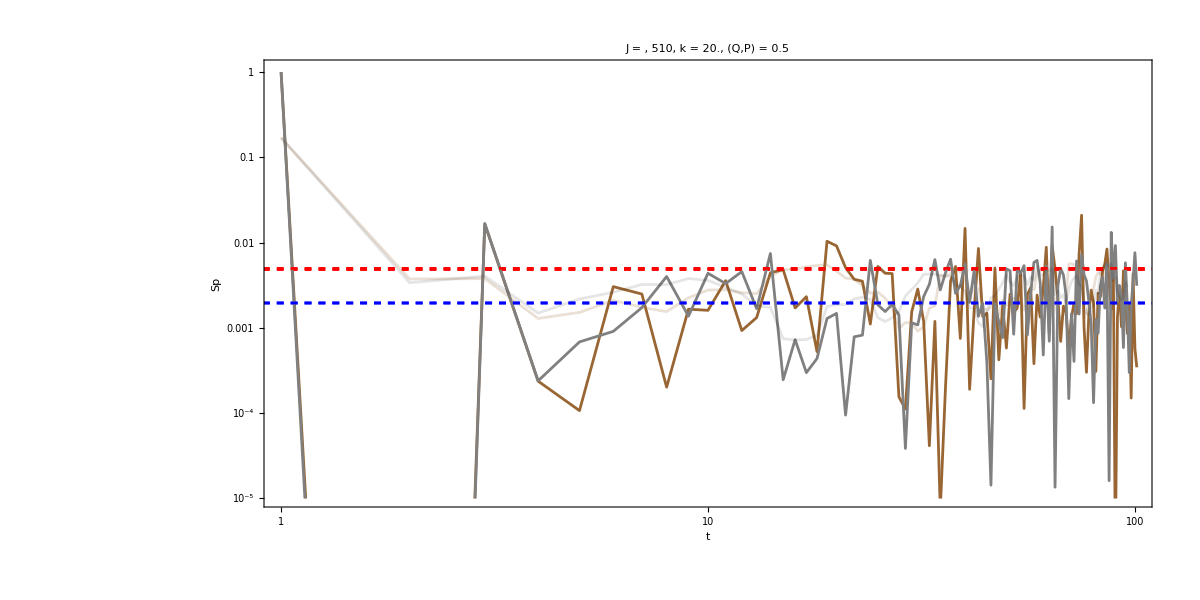

```mathematica
Show[{survival2,survival100}]
```